## Averaged System Without π in the Frequency

To compute the period, which we found earlier to be equivalent to 1/sbar, we integrate the theta model directly assuming that s_x,s_yare constant. In this integration, we multiply the input current term by π^2 to remove the π term in the frequency.

```mathematica
(* compute period, 1/sbar *)
Integrate[1/((1-Cos[x]+(1+Cos[x])(a+b sx-c sy))Pi),{x,0,2*Pi}]
```

$Aborted

With this choice of parameters, the averaged system becomes

```mathematica
Subscript[s, x]'=ϵ(-Subscript[s, x]+√(Subscript[a, 1]+Subscript[b, 1] Subscript[s, x]-Subscript[c, 1] Subscript[s, y]))/Subscript[μ, x],
Subscript[s, y']=ϵ(-Subscript[s, y]+√(Subscript[a, 2]+Subscript[b, 2] Subscript[s, x]-Subscript[c, 2] Subscript[s, y]))/Subscript[μ, y].
```

For this system, we assume WLOG that s̄=1 so we require we may compute the fixed point of the averaged system s_x',s_y' by hand.

```mathematica
Subscript[a, 1]+Subscript[b, 1]-Subscript[c, 1]=1,
Subscript[a, 2]+Subscript[b, 2]-Subscript[c, 2]=1.
```

This choice of new parameters allows for a much broader range of values and even allows for the existence of a supercritical hopf.

Given the Jacobian matrix, we find that the trace and determinant are

```mathematica
Tr J=-1+Subscript[b, 1]/2+1/τ(-1-Subscript[c, y]/2)
det J=1/(4τ)(Subscript[b, 2] Subscript[c, 1]-Subscript[b, 1] Subscript[c, 2]+2 Subscript[c, 2]-2 Subscript[b, 1]+4)
```

```mathematica
Solve[{2==(b1-c1)+Sqrt[(b1-c1)^2+4a1]},{a1}]
```

{{a1→1-b1+c1}}

a1 | b1 | c1 | a2 | b2 | c2 | τ | tr | det | tr^2-4det
0.5 | 10. | 9.5 | 0.5 | 5. | 4.5 | 5 | 3.35 | -0.225 | 12.1225

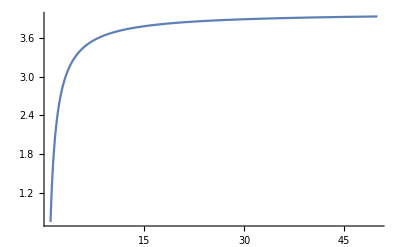

```mathematica
(* determine third coefficient to force same frequency and fixed point at (1,1) *)
aa1=.5;bb1=10.;
cc1=Solve[a1+b1-c1==1/.a1->aa1/.b1->bb1,c1][[All,1,2]][[1]];

aa2=.5;bb2=5.0;
cc2=Solve[a2+b2-c2==1/.a2->aa2/.b2->bb2,c2][[All,1,2]][[1]];

ττ=5;

(* trace and det *)
tr=-1+b1/2+(-1-c2/2)/τ/.b1->bb1/.c2->cc2/.τ->ττ;
det=(b2 c1-b1 c2+2 c2-2 b1+4)/(4 τ)/.b1->bb1/.b2->bb2/.c1->cc1/.c2->cc2/.τ->ττ;

(* data table *)
Grid[{{"a1","b1","c1","a2","b2","c2","τ","tr","det","tr^2-4det"},{aa1,bb1,cc1,aa2,bb2,cc2,ττ,tr,det,tr^2-4det}},Frame->All]

(* for these parameters, plot tr as a function of tau *)
Plot[-1+b1/2+(-1-c2/2)/τ/.b1->bb1/.c2->cc2,{τ,1,50},PlotRange->All]
```

## Original system

```mathematica
sbar [a_,b_,c_]:=(b-c+√((b-c)^2+4 a π^2))/(2 π^2);
```

```mathematica
sbar[1,1,1]
```

1/π

```mathematica
Solve[{x==Sqrt[a+b x-c y]/Pi,y==Sqrt[a+b x-c y]/Pi},{x,y}]
```

{{x→(b-c-√(b^2-2 b c+c^2+4 a π^2))/(2 π^2),y→(b-c-√(b^2-2 b c+c^2+4 a π^2))/(2 π^2)},{x→(b-c+√(b^2-2 b c+c^2+4 a π^2))/(2 π^2),y→(b-c+√(b^2-2 b c+c^2+4 a π^2))/(2 π^2)}}